```mathematica
Z=1;
a0 = 5.29177210544×10^-11;   (*Bohr radius *)
c=299792458; (* Speed of light *)
Eh=4.3597447222060*10^−18;
Ry =Eh/2; (* Rydberg energy *) 
hbar=1.054571817*10^−34;
h=6.62607015*10^−34;
```

```mathematica
Get["D:\\thesis\\mathematica\\dipole_moments\\dipolemoments.m"];
```

```mathematica
Radialdpup[n_, l_, W_,lprime_] := Module[{gValue, lmax,k},
    lmax = Max[l, lprime];
k=Sqrt[W/Ry];
    gValue = gup[n-l][n, k]/Sqrt[Rho[k]]; 
    (* Full formula *)
   gValue
]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

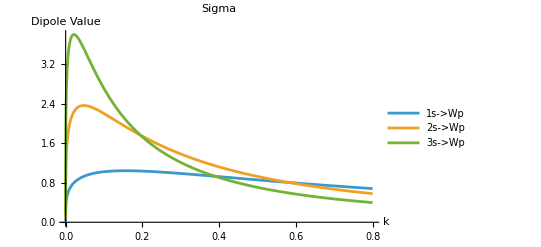

```mathematica
Plot[Evaluate[{Radialdpup[1,0,W Ry,1],Radialdpup[2,0,W Ry,1],Radialdpup[3,0,W Ry,1]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

```mathematica
Plot[Evaluate[{Radialdpup[1,0,W Ry,1],Radialdpup[2,0,W Ry,1],Radialdpup[3,0,W Ry,1]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

```mathematica
Radialgup[n_, l_, W_,lprime_] := Module[{gValue, lmax,k},
    lmax = Max[l, lprime];
k=Sqrt[W/Ry];
    gValue = gup[n-l][n, k]; 
    (* Full formula *)
   gValue
]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

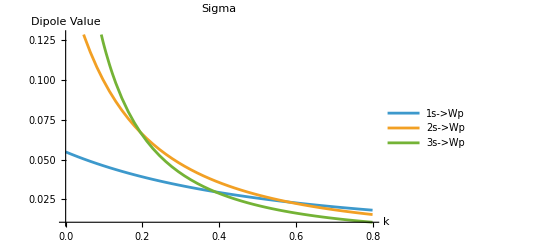

```mathematica
Plot[Evaluate[{Radialgup[1,0,W Ry,1],Radialgup[2,0,W Ry,1],Radialgup[3,0,W Ry,1]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

```mathematica
Radialgup2[n_, l_, W_,lprime_] := Module[{gValue, lmax,k},
    lmax = Max[l, lprime];
k=Sqrt[W/Ry];
    gValue = gup[n-l][n, k]; 
    (* Full formula *)
   Abs[gValue]^2
]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

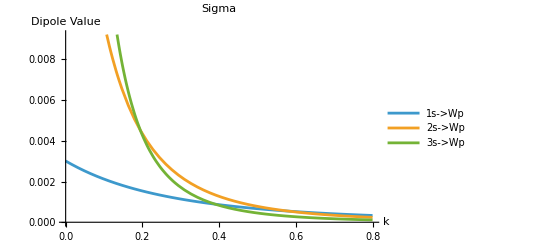

```mathematica
Plot[Evaluate[{Radialgup2[1,0,W Ry,1],Radialgup2[2,0,W Ry,1],Radialgup2[3,0,W Ry,1]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

```mathematica
Sigma1[n_, l_, W_,lprime_] := Module[{gValue, lmax,w},
    lmax = Max[l, lprime];
    w=(W+Ry/n^2)/hbar;
    gValue = gup[n-l][n, Sqrt[W/Ry]]; (*MISTAKE if lprime<l use gdown*)
    (* Full formula *)
   w * Abs[gValue]^2
]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

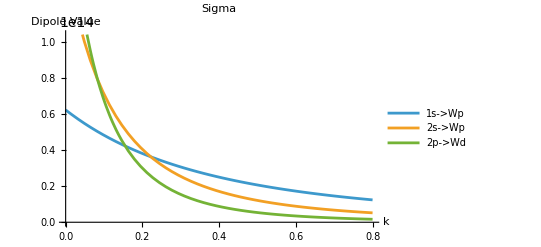

```mathematica
Plot[Evaluate[{Sigma1[1,0,W* Ry,1],Sigma1[2,0,W *Ry,1],Sigma1[2,1,W* Ry,2]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","2p->Wd"},
 PlotRange ->{Automatic, Automatic}]
```

```mathematica
Sigma[n_, l_, W_,lprime_] := Module[{gValue, lmax,w},
    lmax = Max[l, lprime];
    w=(W+Ry/n^2)/hbar;
    gValue = gup[n-l][n, Sqrt[W/Ry]]; (*MISTAKE if lprime<l use gdown*)
    (* Full formula *)
   (4*π^2*w*a0*2*Ry)/(3*c) *10^4 (lmax/(2*l + 1))* Abs[gValue]^2
]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

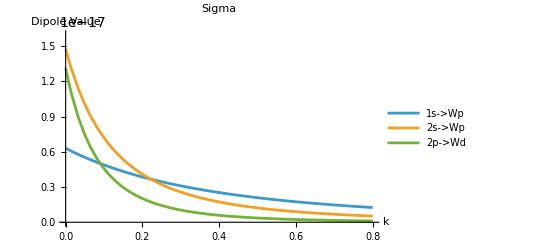

```mathematica
Plot[Evaluate[{Sigma[1,0,W* Ry,1],Sigma[2,0,W *Ry,1],Sigma[2,1,W* Ry,2]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","2p->Wd"},
 PlotRange ->{Automatic, {0,16*10^-18}}]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

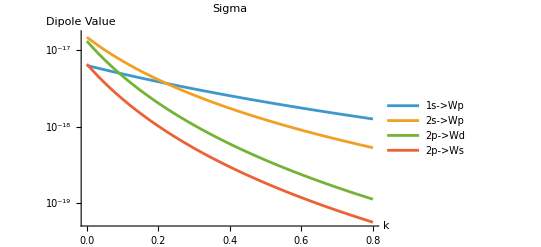

```mathematica
LogPlot[Evaluate[{Sigma[1,0,W* Ry,1],Sigma[2,0,W *Ry,1],Sigma[2,1,W* Ry,2],Sigma[2,1,W *Ry,0]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","2p->Wd","2p->Ws"},
 PlotRange ->{Automatic, {0,16*10^-18}}]
```

```mathematica
g0[n_] := Sqrt[1/(2*(2n-1)!)]*4*(4n)^n*Exp[-2n]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-9829.83] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

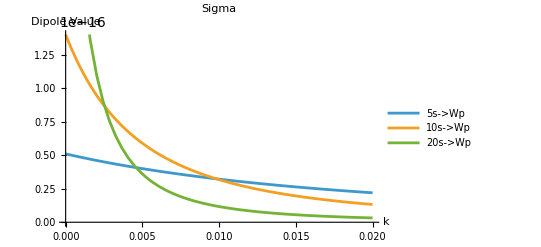

```mathematica
PP=Plot[Evaluate[{Sigma[5,0,W Ry,1],Sigma[10,0,W Ry,1],Sigma[20,0,W Ry,1]}], {W, 0, 0.02},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"5s->Wp","10s->Wp","20s->Wp"},
 PlotRange ->{Automatic, {0,14*10^-17}}]
```

```mathematica
cm = 72/2.54 ;(* centimetre *)
Export["Exports/DT_M5s10s20s_v3.png",PP, "png",ImageResolution -> 300]
```

Exports/DT_M5s10s20s_v3.png

```mathematica
eE0=Sqrt[h];
Ei[i_]:=-Ry/i^2;
ωi[i_]:=Ei[i]/h;
(*T[w_]:=100;*)
SumPWOmega2up[n_, l_, W_]:=eE0^2*n^4/Z^4*Sum[((l+1)^2-m^2)/(4(l+1)^2-1),{m,-l,l}]* Abs[gup[n-l][n, Sqrt[W/Ry]]]^2;
SumPWOmega2down[n_, l_, W_]:=eE0^2*n^4/Z^4*Sum[(l^2-m^2)/(4l^2-1),{m,-l,l}]* Abs[gdown[n-l][n, Sqrt[W/Ry]]]^2;
```

```mathematica
sincTerm[W_, ω_,i_,T_] := Sinc[((W- Ei[i])/h - ω)/2 * T]^2
```

```mathematica
ωmin = 0;
ωmax =- 1.5*Ei[1]/h;
```

Case 1

```mathematica
integrand[W_, ω_,T_] :=  T^2/(2*hbar^2) (SumPWOmega2up[1, 0, W]sincTerm[W, ω,1,T]+SumPWOmega2up[2, 0, W]sincTerm[W,ω,2,T])

Pni[ω_?NumericQ, T_?NumericQ] := NIntegrate[integrand[W, ω,T], {W, 0, (ω+10*2Pi/T)h}]
```

```mathematica
(* Plot range *)

data1 = Table[{ω, Pni[ω,-8Pi h/Ei[1]]}, {ω, ωmin, ωmax, (ωmax - ωmin)/100}]; (* 100 points *)
(*Export["Pni_data_M=2T=100_v0.wl", data, "WL"];  Wolfram Language format *)
```

```mathematica
Ei[1]/4
```

-5.44968×10^-19

```mathematica
Plot[integrand[0,ω,-8Pi h/Ei[1]], {ω, ωmin,ωmax}]
```

-Graphics-

General::munfl: Exp[-1135.05] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

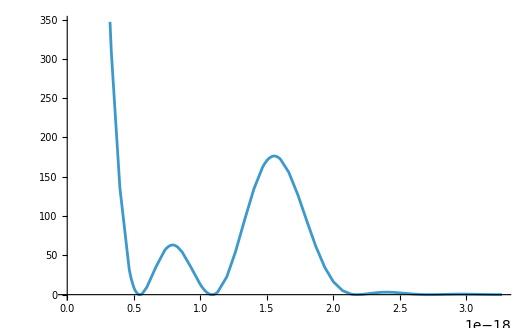

```mathematica
Plot[integrand[W,-Ei[1]/h,-8Pi h/Ei[1]], {W, 0, (ωmax)h},PlotRange ->{Automatic,Automatic}]
```

```mathematica
(* Plot Pni(ω) *)
P = Labeled[
  ListPlot[data1, 
 ImageSize -> 600,Joined -> True],
  Style["ω",  FontSize -> 20],
  Bottom
]
```

-Graphics-ω

```mathematica
cm = 72/2.54 ;(* centimetre *)
Export["Exports/IP_M1s2sT=E1by4E0e=sqrth_v3.png",P, "png",ImageResolution -> 300]
```

Exports/IP_M1s2sT=E1by4E0e=sqrth_v3.png

```mathematica
ωmin = 0;
ωmax =- 1.5*Ei[0];
data2 = Table[{ω, Pni[ω,1000]}, {ω, ωmin, ωmax, (ωmax - ωmin)/100}]; (* 100 points *)
Export["Pni_data_M=2_v0.wl", data2, "WL"]; (* Wolfram Language format *)
```

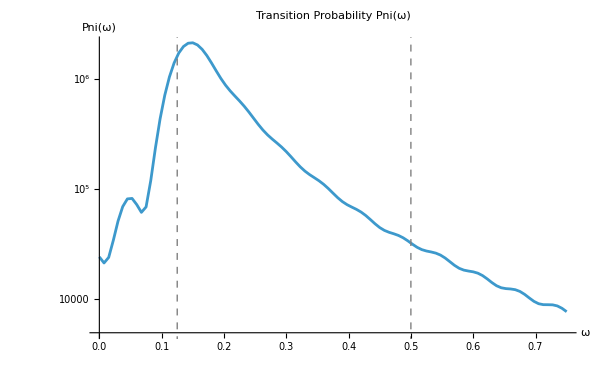

```mathematica
ListLogPlot[data2, 
 PlotLabel -> "Transition Probability Pni(ω)",
 AxesLabel -> {"ω", "Pni(ω)"},
 GridLines -> Automatic,
 ImageSize -> 600,Joined -> True,
Epilog->Table[{Gray, Dashed, Line[{{1/(2*i^2), 0}, {1/(2*i^2), 40000}}]},{i,M}]] (* Control recursion depth *)
```

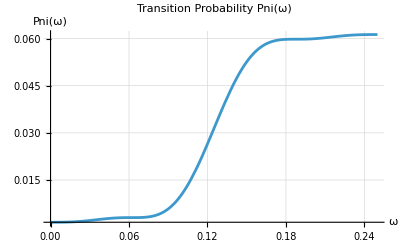

```mathematica
(* Constants and Parameters *)
i = 2;                     (* Defined i *)
Ei =- 1/(2*i^2);             (* Defined E_i *)
Γ23 = Gamma[2/3];          (* Gamma function *)
T[ω_] := 100;             (* T depends on omega *)
E0e = 1;

(* Prefactor term - using En instead of E to avoid conflict *)
prefactor[En_] := 1

(* Sinc-squared term *)
sincTerm[En_, ω_] := Sinc[(En - Ei - ω)/2 * T[ω]]^2

(* Full integrand *)
integrand[En_, ω_] := 1 * prefactor[En] * sincTerm[En, ω]

(* Numerical integration for Pni(ω) *)
Pni[ω_?NumericQ] := NIntegrate[integrand[En, ω], {En, 0, ∞}]

(* Plot range *)
ωmin = 0;
ωmax = -2*Ei;

(* Plot Pni(ω) *)
Plot[Pni[ω], {ω, ωmin, ωmax}, 
 PlotLabel -> "Transition Probability Pni(ω)",
 AxesLabel -> {"ω", "Pni(ω)"},
 PlotRange -> All,
 GridLines -> Automatic,
 PlotPoints -> 30, (* Increase sampling for smoother plot *)
 MaxRecursion -> 3] (* Control recursion depth *)
```